```mathematica
l[a_,b_,c_,d_,e_,f_,g_,h_]:=h+Sum[x,{x,18-e-f-g,18-e-f}]+Sum[Sum[y,{y,0,x}]+1,{x,18-e-f,18-e}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,18-e,18}]-1350+4846*(d+Sum[x,{x,22-a-b-c,22-a-b}]+Sum[Sum[y,{y,0,x}]+1,{x,22-a-b,22-a}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,22-a,22}]-2324)
```

```mathematica
l[0,0,0,1,0,0,0,0]
```

4845

```mathematica
23!/16!/24
```

51482970

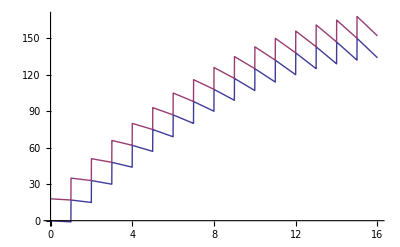

```mathematica
Plot[{l[0,0,0,0,0,0,x,0],Sum[y,{y,18-x,18}]},{x,0,16}]
```

```mathematica
m[a_,b_,c_,d_,e_,f_,g_,h_]:=h+Sum[x,{x,i-e-f-g,i-e-f}]+Sum[Sum[y,{y,0,x}]+1,{x,i-e-f,i-e}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,i-e,i}]-k+4846*(d+Sum[x,{x,j-a-b-c,j-a-b}]+Sum[Sum[y,{y,0,x}]+1,{x,j-a-b,j-a}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,j-a,j}]-l)
```

```mathematica
tmp=Simplify[l[a,b,c,d,e,f,g,h],{a,b,c,d,e,f,g,h}∈Integers]
```

4842-2423/12 (-90 a^3+a^4+a^2 (3035-12 b)-6 a (7575-88 b+2 b^2-4 c)-4 (-66 b^2+b^3+b (1451-6 c)+129 c-3 c^2+6 d))-1/24 (-17+e) (-7104+1094 e-57 e^2+e^3)+1/6 (1+f) (1032+3 e^2+3 e (-37+f)-55 f+f^2)-1/2 (1+g) (-36+2 e+2 f+g)+h

```mathematica
Simplify[l[a,b,c,d,e,f,g,h],{a,b,c,d,e,f,g,h}∈Integers,ComplexityFunction->t]
```

4842+4846 (10623-1/24 (-21+a) (-12456+1598 a-69 a^2+a^3)+1/6 (1+b) (1524+3 a^2+3 a (-45+b)-67 b+b^2)-1/2 (1+c) (-44+2 a+2 b+c)+d)-1/24 (-17+e) (-7104+1094 e-57 e^2+e^3)+1/6 (1+f) (1032+3 e^2+3 e (-37+f)-55 f+f^2)-1/2 (1+g) (-36+2 e+2 f+g)+h

```mathematica
HornerForm[tmp]
```

b (3515773/3+b (-53306+(2423 b)/3)-4846 c)+a (18354225/2+b (-106612+2423 b)+a (-7353805/12+(36345/2-(2423 a)/12) a+2423 b)-4846 c)+(104189-2423 c) c+4846 d+f (971/6+(-9+f/6) f-g)+e (12617/12+e (-2051/24+(37/12-e/24) e+f/2)+(-18+f/2) f-g)+(35/2-g/2) g+h

```mathematica
Simplify[%]
```

-2423/12 a (-90 a^2+a^3+a (3035-12 b)-6 (7575-88 b+2 b^2-4 c))+2423/3 b (1451-66 b+b^2-6 c)-2423 (-43+c) c+4846 d+1/6 f (971-54 f+f^2-6 g)-1/2 (-35+g) g-1/24 e (-25234-74 e^2+e^3+e (2051-12 f)+432 f-12 f^2+24 g)+h

```mathematica
Expand[tmp]
```

(18354225 a)/2-(7353805 a^2)/12+(36345 a^3)/2-(2423 a^4)/12+(3515773 b)/3-106612 a b+2423 a^2 b-53306 b^2+2423 a b^2+(2423 b^3)/3+104189 c-4846 a c-4846 b c-2423 c^2+4846 d+(12617 e)/12-(2051 e^2)/24+(37 e^3)/12-e^4/24+(971 f)/6-18 e f+(e^2 f)/2-9 f^2+(e f^2)/2+f^3/6+(35 g)/2-e g-f g-g^2/2+h

```mathematica
FactorTerms[tmp]
```

1/24 (220250700 a-14707610 a^2+436140 a^3-4846 a^4+28126184 b-2558688 a b+58152 a^2 b-1279344 b^2+58152 a b^2+19384 b^3+2500536 c-116304 a c-116304 b c-58152 c^2+116304 d+25234 e-2051 e^2+74 e^3-e^4+3884 f-432 e f+12 e^2 f-216 f^2+12 e f^2+4 f^3+420 g-24 e g-24 f g-12 g^2+24 h)

```mathematica
PolynomialReduce[tmp]
```

PolynomialReduce::argmu: PolynomialReduce called with 1 argument; 2 or more arguments are expected.

PolynomialReduce[4842-2423/12 (-90 a^3+a^4+a^2 (3035-12 b)-6 a (7575-88 b+2 b^2-4 c)-4 (-66 b^2+b^3+b (1451-6 c)+129 c-3 c^2+6 d))-1/24 (-17+e) (-7104+1094 e-57 e^2+e^3)+1/6 (1+f) (1032+3 e^2+3 e (-37+f)-55 f+f^2)-1/2 (1+g) (-36+2 e+2 f+g)+h]

```mathematica
CForm[%]
```

4842 - (2423*(-90*Power(a,3) + Power(a,4) + Power(a,2)*(3035 - 12*b) - 6*a*(7575 - 88*b + 2*Power(b,2) - 4*c) - 
        4*(-66*Power(b,2) + Power(b,3) + b*(1451 - 6*c) + 129*c - 3*Power(c,2) + 6*d)))/12. - 
   ((-17 + e)*(-7104 + 1094*e - 57*Power(e,2) + Power(e,3)))/24. + 
   ((1 + f)*(1032 + 3*Power(e,2) + 3*e*(-37 + f) - 55*f + Power(f,2)))/6. - ((1 + g)*(-36 + 2*e + 2*f + g))/2. + h

```mathematica
t[x_]:=Tr@((Length[#]-1)&/@(Extract[x,{Sequence@@Drop[#,-1]}]&/@Position[x,Times]))
```

```mathematica
Clear[trial];trial[a_,b_,c_,d_,e_,f_,g_,h_]:=trial[a,b,c,d,e,f,g,h]=If[h==0,If[g==0,If[f==0,If[e==0,If[d==0,If[c==0,If[b==0,If[a==0,0,trial[a-1,21-a,c,d,e,f,g,h]],trial[a,b-1,21-a-b,d,e,f,g,h]],trial[a,b,c-1,21-a-b-c,e,f,g,h]],trial[a,b,c,d-1,17,f,g,h]],trial[a,b,c,d,e-1,17-e,g,h]],trial[a,b,c,d,e,f-1,17-e-f,h]],trial[a,b,c,d,e,f,g-1,17-e-f-g]],trial[a,b,c,d,e,f,g,h-1]]+1;trial[0,0,0,0,0,0,0,0]=0;
```

```mathematica
trial[0,0,0,1,0,0,0,0]=4846;
```

```mathematica
trial[0,0,0,2,0,0,0,0]
```

9692

```mathematica
l[0,0,0,2,0,0,0,0]
```

9692

```mathematica
23!/16!/24
```

51482970

```mathematica
$RecursionLimit=Infinity
```

∞

```mathematica
For[e=0,e≤16,e++,For[f=0,f≤16-e,f++,For[g=0,g≤16-e-f,g++,For[h=0,h≤16-e-f-g,h++,If[l[0,0,0,0,e,f,g,h]≠trial[0,0,0,0,e,f,g,h],Print["Fail"],]]]]]
```

```mathematica
Clear[further];further[a_,b_,c_,d_,e_,f_,g_,h_]:=further[a,b,c,d,e,f,g,h]=If[h==g==f==e==0,If[d==0,If[c==0,If[b==0,If[a==0,0,further[a-1,21-a,c,d,e,f,g,h]],further[a,b-1,21-a-b,d,e,f,g,h]],further[a,b,c-1,21-a-b-c,e,f,g,h]],further[a,b,c,d-1,e,f,g,h]]+4846,further[a,b,c,d,0,0,0,0]+l[a,b,c,d,e,f,g,h]-l[a,b,c,d,0,0,0,0]];further[0,0,0,0,0,0,0,0]=0;
```

```mathematica
further[0,,0,0,0,0,0,0]
```

4627930

```mathematica
l[0,20,0,0,0,0,0,0]/4846
```

1770